```mathematica
f[t_]:=0/;0≤t≤1/3;
f[t_]:=3(t-1/3)/;1/3≤t≤2/3;
f[t_]:=1/;2/3≤t≤1;
f[t_]:=f[-t]/;-1≤t≤0;
f[t_]:=f[t-2]/;t≥2;
f[t_]:=f[t+2]/;t≤-2;
```

```mathematica
FractionalPart
```

```mathematica
ϕ[t_,n_]:=∑_(i=1)^n (1/2^i f[3^(2i-2)t-2IntegerPart[(3^(2i-2)t)/2]])
```

```mathematica
ϕ[t_,n_]:=∑_(i=1)^n (1/2^i f[3^(2i-2)t])
```

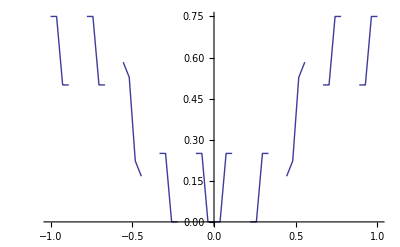

```mathematica
Plot[ϕ[x,2],{x,-1,1}]
```